## Homogeneous resetting using β distribution

## Beta distribution and its moments

```mathematica
P[x_,b_]:=Gamma[b+1/2]/(Sqrt[π]Gamma[b])(1-x^2)^(b-1);
Integrate[P[x,b],{x,-1,1},Assumptions->b>0]
```

1

```mathematica
x1=Integrate[Abs[x]*P[x,b],{x,-1,1},Assumptions->b>0]
x2=Integrate[x^2*P[x,b],{x,-1,1},Assumptions->b>0]
x3=Integrate[Abs[x] x^2*P[x,b],{x,-1,1},Assumptions->b>0]
x4=Integrate[x^4*P[x,b],{x,-1,1},Assumptions->b>0]
```

Gamma[1/2+b]/(b √π Gamma[b])

1/(1+2 b)

Gamma[1/2+b]/(√π Gamma[2+b])

3/(3+4 b (2+b))

## Expansion of average MFPT

### General MFPT for any distribution with homogeneous resetting

```mathematica
τ0[r_,x_]:=r^-1*(Cosh[Sqrt[r]x]-1+(Cosh[Sqrt[r]]-1)Sinh[Sqrt[r]Abs[x]]/Sinh[Sqrt[r]]);
```

```mathematica
Series[τ0[r,xT],{r,0,1}]
```

1/2 (xT^2+Abs[xT])+1/24 (xT^4-Abs[xT]+2 Abs[xT]^3) r+O[r]^(3/2)

### Expansion of of average MFPT for β distribution

```mathematica
FullSimplify[1/2(x2+x1)]
m[b_]:=FullSimplify[(x4-x1+2x3)/24];
```

1/2 (1/(1+2 b)+Gamma[1/2+b]/(√π Gamma[1+b]))

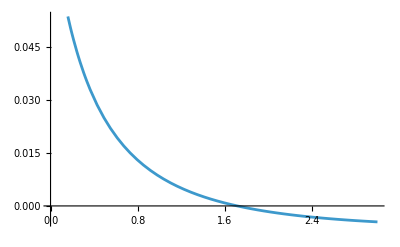

```mathematica
Plot[m[b],{b,0,3}]
```

```mathematica
Limit[m[b],b->∞]
```

0

The change of behaviour (from positive to negative) is attained at

```mathematica
FindRoot[1/(8 (3+4 b (2+b)))-((-1+b) Gamma[1/2+b])/(24 √π Gamma[2+b]),{b,0.1}]
```

{b→1.71339}

### Average MFPT for β distribution

```mathematica
Integrate[P[x,b]τ0[r,x],{x,-1,1},Assumptions->{b>0,r>0}]
```

(-1+Hypergeometric0F1[1/2+b,r/4]+2^(-1/2+b) r^(1/4-b/2) Gamma[1/2+b] StruveL[-1/2+b,√r] Tanh[(√r)/2])/r

```mathematica
τBarBeta[r_,b_]:=(-1+Hypergeometric0F1[1/2+b,r/4]+2^(-1/2+b) r^(1/4-b/2) Gamma[1/2+b] StruveL[-1/2+b,√r] Tanh[(√r)/2])/r;
```

```mathematica
Manipulate[Plot[τBarBeta[r,b],{r,0,100}],{b,0,10}]
```

Expansion of the average MFPT; consistency with average of the expansion

```mathematica
FullSimplify[Series[τBarBeta[r,b],{r,0,1}]]
```

1/4 (1/(1/2+b)+(2 Gamma[1/2+b])/(√π Gamma[1+b]))+(1/(8 (3+4 b (2+b)))-((-1+b) Gamma[1/2+b])/(24 √π Gamma[2+b])) r+O[r]^(5/4)

### Roots of M(x_T)

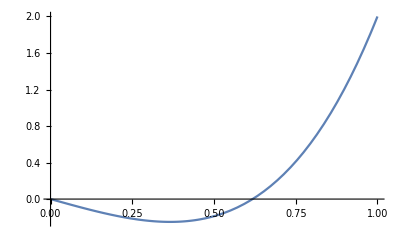

```mathematica
Plot[x^4-Abs[x](1-2 x^2),{x,0,1}]
```

```mathematica
Solve[x^4-Abs[x](1-2 x^2)==0,x]
```

{{x→0},{x→1/2 (1-√5)},{x→1/2 (-1+√5)}}

```mathematica
N[1/2 (√5-1)]
```

0.618034